```mathematica
f[r_,x_,y_]:=Exp[-(x^2+y^2)/r^2];
```

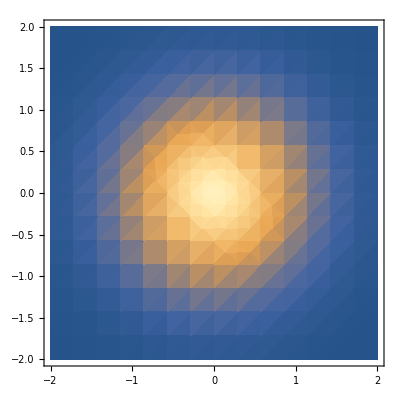

```mathematica
r=1; DensityPlot[f[r,x,y],{x,-2,2},{y,-2,2}]
```

```mathematica
Plot3D[f[r,x,y],{x,-2,2},{y,-2,2}]
```

-Graphics3D-

```mathematica
Plot1=Plot3D[f[1,x,y],{x,-5,5},{y,-5,5}];
Plot2=Plot3D[f[2,x,y],{x,-5,5},{y,-5,5}];
Plot3=Plot3D[f[3,x,y],{x,-5,5},{y,-5,5}];
Plot4=Plot3D[f[4,x,y],{x,-5,5},{y,-5,5}];
Plot4
GraphicsGrid[{{Plot1,Plot2,Plot4},
{Plot1,Plot2,Plot4}}]
```

-Graphics3D-

-Graphics-